```mathematica
f = SystemDialogInput["FileOpen"]
```

```mathematica
f = "K:\\Dropbox\\2015_03_30b.csv"
```

K:\Dropbox\2015_03_30b.csv

```mathematica
textdata = Import[f];
```

```mathematica
numdata = ToExpression[
	StringReplace[#,{" "-> "", "Cdeg"-> "", "V" -> ""}]&/@ textdata[[2;;]]
];
```

```mathematica
caldata = Transpose[
	{numdata[[All,1]]-273.15,numdata[[All,3]]/numdata[[All,2]]}
];
```

#### Specify the Initial Curve P(t)

```mathematica
cpoints ={{-50,0.6},{-20,0.64},{0,0.65},{10.00,0.660},{20,0.69},{30,0.71},{50,0.74},{100,0.82},{200,0.94},{300,1.06},{400,1.17},{500,1.27}}
```

{{-50,0.6},{-20,0.64},{0,0.65},{10.,0.66},{20,0.69},{30,0.71},{50,0.74},{100,0.82},{200,0.94},{300,1.06},{400,1.17},{500,1.27}}

```mathematica
P=BSplineFunction[cpoints]
```

BSplineFunction[…]

```mathematica
fitdata = caldata[[Range[npoints]*10]];
```

```mathematica
npoints = 5090 ;(* In the example data set there are 50903 data points *)
```

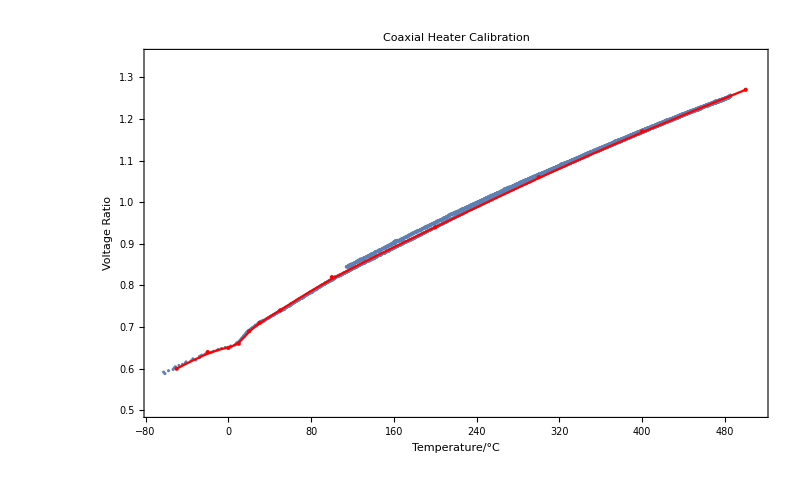

```mathematica
cplot = Show[ListPlot[fitdata
	, AxesLabel->{"Temperature (°C)", "Voltge Ratio"}
	, PlotLabel->Style["Coaxial Heater Calibration", Black, 20]
	, PlotRange -> {{-70,510}, {0.5,1.35}}
	, ImageSize-> 800
	, Axes->False
	, Frame->True
	, FrameLabel->{Style["Temperature/°C", Black, 15]
				,Style["Voltage Ratio", Black,15]}
	,FrameTicksStyle->15
		]
, Graphics[{Red, PointSize[Large],Point[cpoints]}]
,ParametricPlot[P[t],{t,0,1}, PlotStyle->{Red}]
(*, ListPlot[fp, PlotStyle->{Black}]*)
]
```

```mathematica
outfile1 =StringJoin[NotebookDirectory[],FileBaseName[NotebookFileName[]], " CPlot.pdf"]
```

K:\Dropbox\2019_07_12 B-spline fit CPlot.pdf

```mathematica
Export[outfile1, cplot]
```

K:\Dropbox\2019_07_12 B-spline fit CPlot.pdf

Sample points from the B-Spline:

```mathematica
spoints = Table[P[x], {x,(Range[21]-1)/20.0}]
```

{{-50.,0.6},{-20.1312,0.635851},{-5.45,0.647858},{2.58458,0.653414},{7.97333,0.6597},{12.5,0.66888},{17.,0.680518},{21.5056,0.691982},{26.36,0.702253},{32.4296,0.71293},{40.8333,0.72625},{53.2871,0.745645},{71.6133,0.774227},{97.6346,0.812122},{132.858,0.858287},{175.13,0.910104},{220.067,0.96406},{267.289,1.02006},{321.125,1.08201},{391.578,1.15892},{500.,1.27}}

```mathematica
TableForm[Reverse[spoints]]
```

500. | 1.27
391.578 | 1.15892
321.125 | 1.08201
267.289 | 1.02006
220.067 | 0.96406
175.13 | 0.910104
132.858 | 0.858287
97.6346 | 0.812122
71.6133 | 0.774227
53.2871 | 0.745645
40.8333 | 0.72625
32.4296 | 0.71293
26.36 | 0.702253
21.5056 | 0.691982
17. | 0.680518
12.5 | 0.66888
7.97333 | 0.6597
2.58458 | 0.653414
-5.45 | 0.647858
-20.1312 | 0.635851
-50. | 0.6

```mathematica
fip = Interpolation[spoints]
```

InterpolatingFunction[{{-50., 500.}}, <>]

```mathematica
dfip = fip'[spoints[[All,1]] ]
```

{0.00153333,0.000918606,0.000564415,0.000851599,0.00156472,0.00234336,0.00266493,0.00240297,0.00193227,0.00163159,0.00161384,0.00164407,0.00158106,0.00134695,0.00125358,0.00120114,0.00119148,0.00117272,0.00112798,0.00105154,0.000992233}

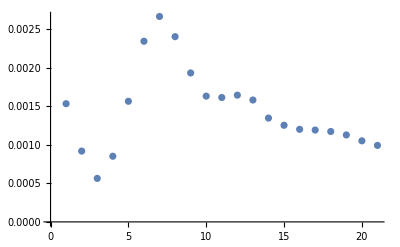

```mathematica
ListPlot[dfip]
```

```mathematica
dpolypoints =Join[Map[List, Split[spoints[[All,1]] ]],Split[spoints[[All,2]]], Split[dfip], 2]
```

{{{-50.},0.6,0.00153333},{{-20.1312},0.635851,0.000918606},{{-5.45},0.647858,0.000564415},{{2.58458},0.653414,0.000851599},{{7.97333},0.6597,0.00156472},{{12.5},0.66888,0.00234336},{{17.},0.680518,0.00266493},{{21.5056},0.691982,0.00240297},{{26.36},0.702253,0.00193227},{{32.4296},0.71293,0.00163159},{{40.8333},0.72625,0.00161384},{{53.2871},0.745645,0.00164407},{{71.6133},0.774227,0.00158106},{{97.6346},0.812122,0.00134695},{{132.858},0.858287,0.00125358},{{175.13},0.910104,0.00120114},{{220.067},0.96406,0.00119148},{{267.289},1.02006,0.00117272},{{321.125},1.08201,0.00112798},{{391.578},1.15892,0.00105154},{{500.},1.27,0.000992233}}

```mathematica
pip = InterpolatingPolynomial[dpolypoints, x]
```

1.27+(-500.+x) (0.000992233+(-500.+x) (-4.10816×10^-7+(50.+x) (2.94877×10^-10+(50.+x) (-3.8996×10^-13+(-220.067+x) (-1.52135×10^-15+(-220.067+x) (1.9141×10^-17+(-391.578+x) (-2.87253×10^-19+(-391.578+x) (-1.98972×10^-21+(-40.8333+x) (2.85784×10^-23+(-40.8333+x) (-1.45603×10^-25+(-132.858+x) (8.1534×10^-30+(-132.858+x) (1.52471×10^-30+(-321.125+x) (-1.49095×10^-32+(-321.125+x) (-1.03204×10^-34+(20.1312+x) (-1.18864×10^-35+(20.1312+x) (4.59727×10^-38+(-267.289+x) (-2.2395×10^-40+(-267.289+x) (-2.58972×10^-41+(-7.97333+x) (-1.84329×10^-43+(-7.97333+x) (2.00853×10^-45+(-175.13+x) (-2.10237×10^-47+(-175.13+x) (4.7772×10^-49+(-71.6133+x) (-7.96931×10^-51+(-71.6133+x) (1.32238×10^-53+(-97.6346+x) (-3.40457×10^-55+(-97.6346+x) (-1.54514×10^-57+(5.45+x) (9.32631×10^-58+(2.1983×10^-58+(-9.81626×10^-60+(8.3984×10^-62+(2.5522×10^-62+(3.84853×10^-64+(3.63144×10^-67+(3.479×10^-66+(-1.77273×10^-67+(6.60792×10^-69+(7.51262×10^-71+(1.96587×10^-70+(-1.32694×10^-70+(1.57255×10^-71+1.02201×10^-72 (-21.5056+x)) (-12.5+x)) (-12.5+x)) (-32.4296+x)) (-32.4296+x)) (-17.+x)) (-17.+x)) (-2.58458+x)) (-2.58458+x)) (-53.2871+x)) (-53.2871+x)) (-26.36+x)) (-26.36+x)) (5.45+x))))))))))))))))))))))))))))

```mathematica
ListPlot[dpolypoints[[All,{1,2}]]]
```

-Graphics-

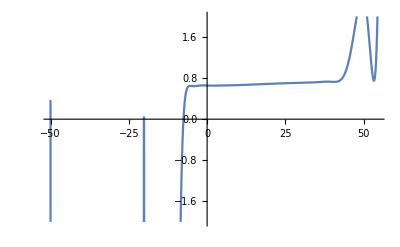

```mathematica
Plot[pip, {x, -50, 500}, PlotRange->{All,{-2,2}}]
```

```mathematica
pip /.x ->50
```

2.3544

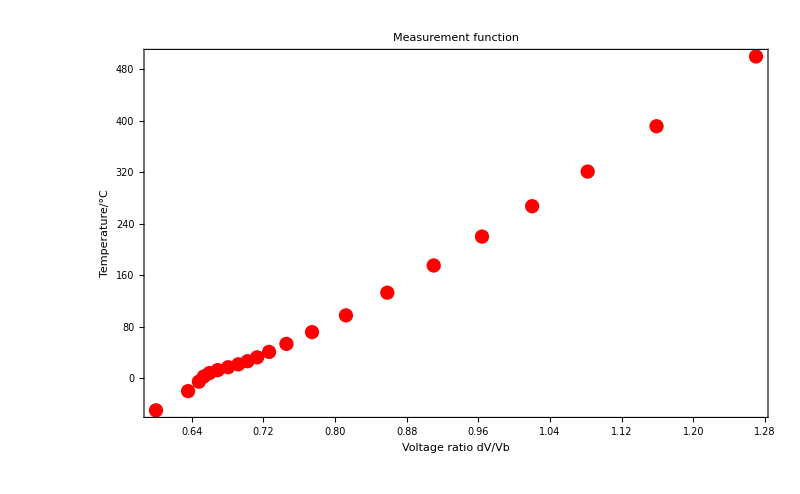

```mathematica
pplot = Show[
ListPlot[Reverse[spoints,2], PlotStyle-> Red, AxesLabel-> {"Voltage Ratio", "Temperature"}]
	,Axes-> False
	,Frame->True
	, PlotLabel-> Style["Measurement function", Black, 20]
	, ImageSize-> 800
	, FrameLabel->{Style["Voltage ratio dV/Vb", Black, 15, Bold]
		,Style["Temperature/°C", Black, 15, Bold]}
]
```

```mathematica
outfile2 =StringJoin[NotebookDirectory[],FileBaseName[NotebookFileName[]], " PPlot.pdf"]
```

K:\Dropbox\2019_07_12 B-spline fit PPlot.pdf

```mathematica
Export[outfile2, pplot]
```

K:\Dropbox\2019_07_12 B-spline fit PPlot.pdf

```mathematica
ListPlot[Reverse[spoints,2], PlotStyle-> Red,]
```

ListPlot::nonopt: Options expected (instead of Null) beyond position 1 in ListPlot[« 1 »]. An option must be a rule or a list of rules.

ListPlot[{{0.6,-50.},{0.635851,-20.1312},{0.647858,-5.45},{0.653414,2.58458},{0.6597,7.97333},{0.66888,12.5},{0.680518,17.},{0.691982,21.5056},{0.702253,26.36},{0.71293,32.4296},{0.72625,40.8333},{0.745645,53.2871},{0.774227,71.6133},{0.812122,97.6346},{0.858287,132.858},{0.910104,175.13},{0.96406,220.067},{1.02006,267.289},{1.08201,321.125},{1.15892,391.578},{1.27,500.}},PlotStyle→RGBColor[1, 0, 0],Null]